```mathematica
uTrue[x_,y_]:=1+Sin[Pi (1+x) ((1+y)^2) 0.125]
```

```mathematica
epsi=1
```

1

```mathematica
a ={{epsi*Exp[-20*Sqrt[x^2+y^2]],0},{0,epsi*Exp[-20*Sqrt[x^2+y^2]]}}
b = {2-y^2,2-x}
c=(1+x)(1+y)^2
```

{{ⅇ^(-20 √(x^2+y^2)),0},{0,ⅇ^(-20 √(x^2+y^2))}}

{2-y^2,2-x}

(1+x) (1+y)^2

List(List(Power(E,-20*Sqrt(Power(x,2) + Power(y,2))),0),List(0,Power(E,-20*Sqrt(Power(x,2) + Power(y,2)))))

```mathematica
nANablaU = {1,0}.a.Grad[uTrue[x,y],{x,y}]
```

0.+0.392699 ⅇ^(-20 √(x^2+y^2)) (1+y)^2 Cos[0.392699 (1+x) (1+y)^2]

```mathematica
CForm[nANablaU]
```

0. + (0.39269908169872414*Power(1 + y,2)*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)))/Power(E,20*Sqrt(Power(x,2) + Power(y,2)))

```mathematica
fExpression= -Div[a.Grad[uTrue[x,y],{x,y}], {x,y}] + Div[Times[b,uTrue[x,y]],{x,y}] + Times[c,uTrue[x,y]]
```

-0.785398 ⅇ^(-20 √(x^2+y^2)) (1+x) Cos[0.392699 (1+x) (1+y)^2]+0.785398 (2-x) (1+x) (1+y) Cos[0.392699 (1+x) (1+y)^2]+0.392699 (1+y)^2 (2-y^2) Cos[0.392699 (1+x) (1+y)^2]+(15.708 ⅇ^(-20 √(x^2+y^2)) (1+x) y (1+y) Cos[0.392699 (1+x) (1+y)^2])/(√(x^2+y^2))+(7.85398 ⅇ^(-20 √(x^2+y^2)) x (1+y)^2 Cos[0.392699 (1+x) (1+y)^2])/(√(x^2+y^2))+0.61685 ⅇ^(-20 √(x^2+y^2)) (1+x)^2 (1+y)^2 Sin[0.392699 (1+x) (1+y)^2]+0.154213 ⅇ^(-20 √(x^2+y^2)) (1+y)^4 Sin[0.392699 (1+x) (1+y)^2]+(1+x) (1+y)^2 (1+Sin[0.392699 (1+x) (1+y)^2])

```mathematica
f[x_,y_]:=Evaluate[fExpression]
```

```mathematica
CForm[fExpression]
```

(-0.7853981633974483*(1 + x)*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)))/Power(E,20*Sqrt(Power(x,2) + Power(y,2))) + 
   0.7853981633974483*(2 - x)*(1 + x)*(1 + y)*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)) + 
   0.39269908169872414*Power(1 + y,2)*(2 - Power(y,2))*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)) + 
   (15.707963267948966*(1 + x)*y*(1 + y)*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)))/(Power(E,20*Sqrt(Power(x,2) + Power(y,2)))*Sqrt(Power(x,2) + Power(y,2))) + 
   (7.853981633974483*x*Power(1 + y,2)*Cos(0.39269908169872414*(1 + x)*Power(1 + y,2)))/(Power(E,20*Sqrt(Power(x,2) + Power(y,2)))*Sqrt(Power(x,2) + Power(y,2))) + 
   (0.6168502750680849*Power(1 + x,2)*Power(1 + y,2)*Sin(0.39269908169872414*(1 + x)*Power(1 + y,2)))/Power(E,20*Sqrt(Power(x,2) + Power(y,2))) + 
   (0.15421256876702122*Power(1 + y,4)*Sin(0.39269908169872414*(1 + x)*Power(1 + y,2)))/Power(E,20*Sqrt(Power(x,2) + Power(y,2))) + 
   (1 + x)*Power(1 + y,2)*(1 + Sin(0.39269908169872414*(1 + x)*Power(1 + y,2)))

```mathematica
CForm[uTrue[x,y]]
```

1 + Sin(0.39269908169872414*(1 + x)*Power(1 + y,2))

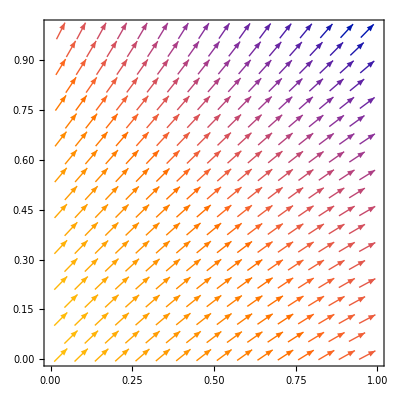

```mathematica
VectorPlot[b,{x,0,1},{y,0,1}]
```

```mathematica
nan=Transpose[{x,y}].a.{x,y}
```

ⅇ^(-20 √(x^2+y^2)) x^2+ⅇ^(-20 √(x^2+y^2)) y^2

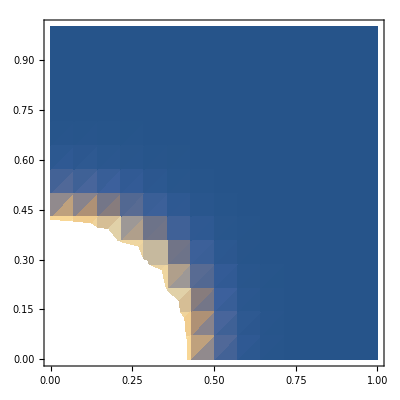

```mathematica
DensityPlot[Transpose[{0,-1}].a.{0,-1},{x,0,1},{y,0,1}]
```

```mathematica
DensityPlot[Transpose[{0,1}].a.{0,1},{x,0,1},{y,0,1}]
```

-Graphics-

```mathematica
DensityPlot[Transpose[{-1,0}].a.{-1,0},{x,0,1},{y,0,1}]
```

-Graphics-